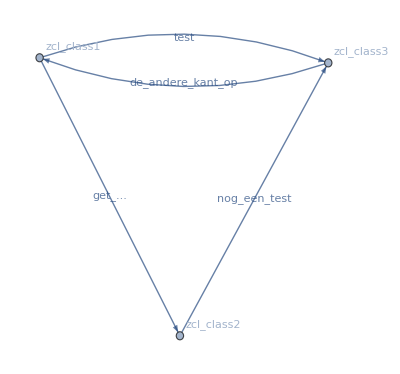

```mathematica
Graph[{Labeled[z1,"zcl_class1"],Labeled[2,"zcl_class2"],Labeled[3,"zcl_class3"]},{Labeled[z1->2,"get_..."],Labeled[z1->3,"test"],Labeled[2->3,"nog_een_test"],Labeled[3->z1,"de_andere_kant_op"]}]
```

```mathematica
e3=Import["/Users/Olaf/Documents/Mathematica/edges.csv"];
l3=First[e3];
l3//InputForm
```

{"zclass1", "zclass2", "method1"}

```mathematica
l3a=ToExpression[l3];
%//InputForm
```

{zclass1, zclass2, method1}

```mathematica
(Labeled[#1->#2,#3]&@@ToExpression[#]&)/@e3
```

{zclass1->zclass2method1,zclass2->zclass1method2}

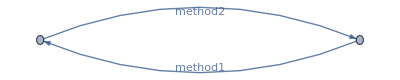

```mathematica
Graph[%]
```

```mathematica
(* CLAS,ZCLASS3,METHOD_A,CLAS,ZCLASS3,METHOD_B *)
file=Import["/Users/Olaf/Documents/Mathematica/edges2.csv"];
line=file[[1]];InputForm[line]
```

{"CLAS", "ZCLASS3", "METHOD_A", "CLAS", "ZCLASS3", "METHOD_B"}

```mathematica
bin=Module[{lastValues=Values[Databin["EZ5uJj4L",-1]]//First},
ImportString[lastValues]];
line=bin[[1]];
InputForm[line]
Databin["EZ5uJj4L"]["LatestDate"]
```

Fri 12 Jul 2019 15:38:42GMT+2.

{"CLAS", "ZCL_ICL_SZ_PROCESS_WIA_CARE", "", "CLAS", "CL_ICL_IIF_PS", ""}

```mathematica
DateObject[{2019,7,12,14,8,59.61106586456299},"Instant","Gregorian",2.]
```

Fri 12 Jul 2019 14:08:59GMT+2.

```mathematica
convertName[s_String]:=ToExpression@StringReplace[ToLowerCase[s],"_"~~x_->ToUpperCase[x]];
convertName["ZCL_SZ_CLASS1"]
```

zclSzClass1

```mathematica
importEdge[{type1_,name1_,comp1_,type2_,name2_,comp2_}]:=
Module[{
vertex1=Tooltip[convertName[name1],ToLowerCase[type1 <> " "<>name1 ]],
vertex2=Tooltip[convertName[name2],ToLowerCase[type2 <> " "<>name2]]},
 (*Tooltip[Labeled[vertex1->vertex2,convertName[comp2]],"From "<>comp1]];*)
(*Labeled[vertex1->vertex2,convertName[comp2]]*)
vertex1->vertex2];
importEdge[line]
```

zclIclSzProcessWiaCare->clIclIifPs

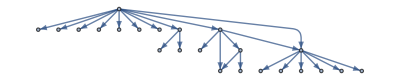

```mathematica
Graph[#[[2]]->#[[5]]&/@bin]
```

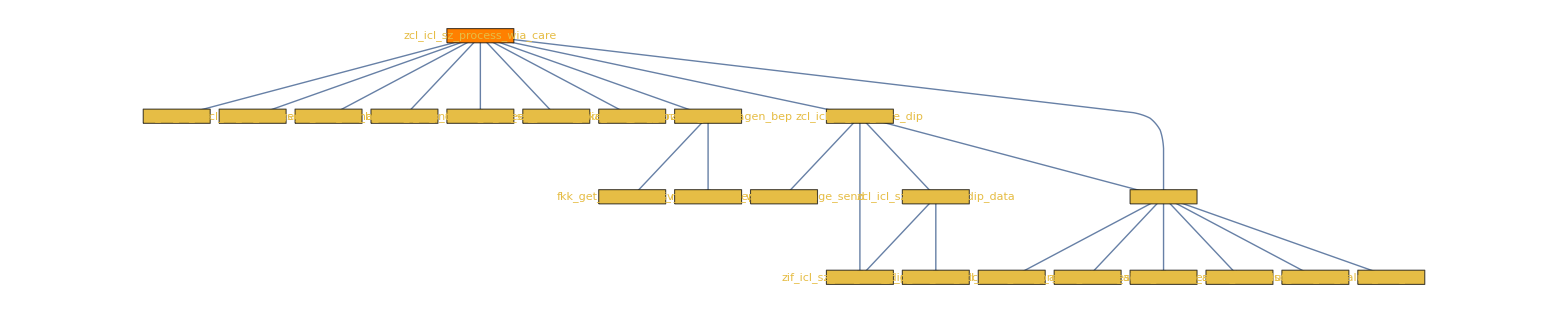

```mathematica
g=Graph[ToLowerCase@#[[2]]->ToLowerCase@#[[5]]&/@bin,
VertexShapeFunction->"Square",
VertexSize->{.5,.1},
VertexLabels->Placed["Name",Center],
VertexStyle->Hue[0.125,0.7,0.9],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->Medium}],
ImageSize->3000];
HighlightGraph[g,{Style["zcl_icl_sz_process_wia_care",Orange]}]
```

```mathematica
Dataset[bin]
```

Dataset[<>]

```mathematica
Databin["EZ5uJj4L"]
```

Databin[…]

```mathematica
Dataset[bin][1;;3]
```

Dataset[<>]